```mathematica
<<Geometry`
```

## Pythagorean Tiling App - In Development

### Functions for lines

```mathematica
ClearAll[lFun1]
lFun1[point1:pnt,point2:pnt]:=Module[{a,b},
{a,b}=LinearSolve[{{point1[[1]],1},{point2[[1]],1}},{point1[[2]],point2[[2]]}];
Print[a];
Print[b];
Function[x,a x+b]
]
lFun1[point1:pnt,r_Real]:=Module[{a,b},
{a,b}={r,point1[[2]]-r point1[[1]]};
Print[a];
Print[b];
Function[x,r x+b]
]
lFun1[{0.25,1},{1,-0.25}][1.75]
```

-1.66667

1.41667

-1.5

```mathematica
17./12
```

1.41667

```mathematica
LinearSolve[{{fr,1},{1,1}},{1,-fr}]
```

{(1+fr)/(-1+fr),(-1-fr^2)/(-1+fr)}

```mathematica
0.25/1.75
```

0.142857

```mathematica
LinearSolve[{{(-1-fr)/(-1+fr),1},{(-1+fr)/(1+fr),1}},{(-1-fr^2)/(-1+fr),0}]
```

{(1+fr)/2,(1-fr)/2}

```mathematica
LinearSolve[{{(-1-fr)/(-1+fr),1},{0,1}},{(-1-fr^2)/(-1+fr),1/2}]
```

{(1+fr+2 fr^2)/(2 (1+fr)),1/2}

```mathematica
(1+.5+2 (.5)^2)/(2+2 .5)
```

0.666667

### Symmetries

### Method

```mathematica
pythagoreanTiling[var_]:=Module[{
pO,pP,pQ,pR,pS,pT,pU,
dPolyA, dPolyB, dPolyC, dPolyD,
dpoly, dpoly1,dpoly2
},
pO={0,0};
pP={(1+var)/2,(1-var)/2};
pQ={(1+var+2 var^2)/(2 (1+var)),1/2};
pR={0.50,0.50};
pS={0.50,(1-var)/(1+var) 0.50};
pT={var,1};
pU={0.50 var,0.50};

dPolyA={{{1,{pP,pQ,pR,pS}},{RGBColor[1, 0.9500000000000001, 0],1}},{RGBColor[1, 0.9500000000000001, 0],1,0.005,2 π,2 π}};
dPolyB={{{1,{pQ,pT,pO,pS,pR}},{RGBColor[1, 0, 0.15],1}},{RGBColor[1, 0, 0.15],1,0.005,2 π,2 π}};
dPolyC={{{1,{pU,pQ}},{RGBColor[0, 0.9500000000000001, 0],1}},{RGBColor[0.05, 0., 0.65],1,0.0025,2 π,2 π}};
dPolyD={{{1,{pR, pS}},{RGBColor[0, 0.9500000000000001, 0],1}},{RGBColor[0.05, 0., 0.65],1,0.0025,2 π,2 π}};

dpoly={dPolyA,dPolyB,dPolyC,dPolyD};
dpoly1=rot3[dpoly,{-ArcTan[pP[[2]]/pP[[1]]],{0,0}}];
dpoly2=sca3[dpoly1,{{1/√((.25)^2+(.75)^2),1/√((.25)^2+(.75)^2)},{0,0}}];
{pO,pP,pQ,pR,pS,pT,pU}
]
```

-0.321751

{{0,0},{0.75,0.25},{0.666667,1/2},{0.5,0.5},{0.5,0.166667},{0.5,1},{0.25,0.5}}

-0.321751

-0.321751

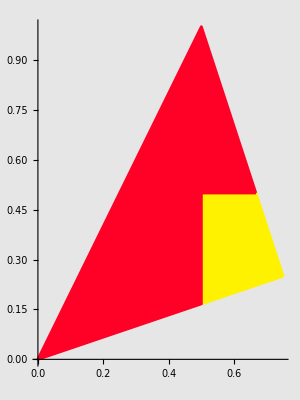

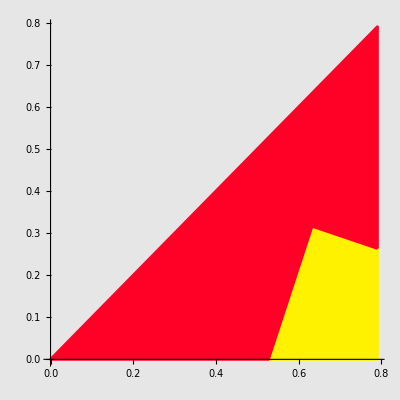

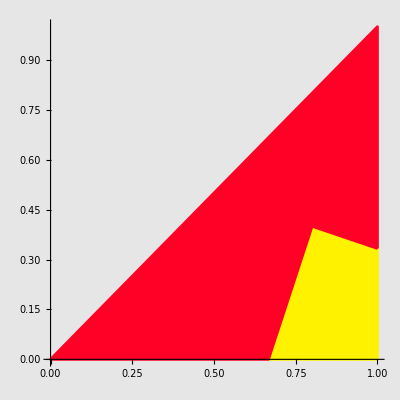

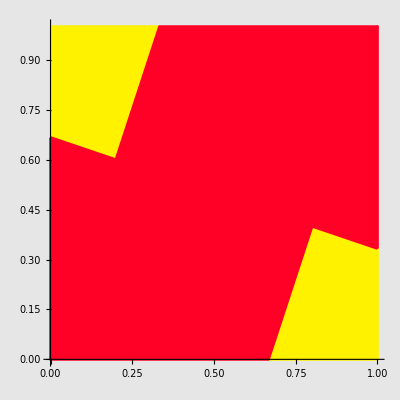

```mathematica
pO={0.0,0.0};
pP={0.75,0.25};
pQ={2./3,0.50};
pR={0.50,0.50};
pS={0.50,1./6};
pT={0.50,1.};
pU={0.25,0.50};

dPolyA:={{{1,{pP,pQ,pR,pS}},{RGBColor[1, 0.9500000000000001, 0],1}},{RGBColor[1, 0.9500000000000001, 0],1,0.005,2 π,2 π}}
dPolyB:={{{1,{pQ,pT,pO,pS,pR}},{RGBColor[1, 0, 0.15],1}},{RGBColor[1, 0, 0.15],1,0.005,2 π,2 π}}
dPolyC:={{{1,{pU,pQ}},{RGBColor[0, 0.9500000000000001, 0],1}},{RGBColor[0.05, 0., 0.65],1,0.0025,2 π,2 π}}
dPolyD:={{{1,{pR, pS}},{RGBColor[0, 0.9500000000000001, 0],1}},{RGBColor[0.05, 0., 0.65],1,0.0025,2 π,2 π}}

dpoly:={dPolyA,dPolyB,dPolyC,dPolyD}
dpoly//toGL//gr2
dpoly1:=rot3[dpoly,{-ArcTan[1/3],{0,0}}]
dpoly1//toGL//gr2
dpoly2:=sca3[dpoly1,{{1/√((.25)^2+(.75)^2),1/√((.25)^2+(.75)^2)},{0,0}}]
dpoly2//toGL//gr2
dpoly3:={dpoly2,rot3[dpoly2,{π,{0.5,0.5}}]}

dpoly3//toGL//gr2
```

```mathematica
Nest[sym4rot,dpoly3,2]//toGL//gr
```

-Graphics-